NT = 11/10, NS = 31/10

TTT = 1, N[TTT] = 1.

CkValList = (NS-NT TTT
NS+NT TTT^2
NS-NT TTT^3
NS+NT TTT^4
NS-NT TTT^5
NS+NT TTT^6)

----------------

----------------

----------------

с6222 = (NS+NT TTT^6)/((NS+NT TTT^2)^3)

с6222 = 1/(NS+NT)^2

с6222 = 25/441

----------------

с532 = (NS-NT TTT^5)/((NS+NT TTT^2) (NS-NT TTT^3))

с532 = 1/(NS+NT)

с532 = 5/21

----------------

с5221 = (NS-NT TTT^5)/((NS-NT TTT) (NS+NT TTT^2)^2)

с5221 = 1/(NS+NT)^2

с5221 = 25/441

----------------

с422 = (NS+NT TTT^4)/((NS+NT TTT^2)^2)

с422 = 1/(NS+NT)

с422 = 5/21

----------------

с112 = (NS-NT TTT)^2/(NS+NT TTT^2)

с112 = (NS-NT)^2/(NS+NT)

с112 = 20/21

----------------

c2 = NS+NT TTT^2

c2 = 21/5

----------------

FindMinimum

sol[[1]] = 0.00811102

xLstSolSorted = {-1.00702,-1.00702,-1.00702,-0.228043,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,-0.000181002,0.236735,1.02171}

M1 = -1.99862, M2 = 4.19422, M3 = -1.99567, M4 = 4.18072, M5 = -1.9933, (M3*M2/M5)*(c5/(c3*c2)) = (0.999808 c5)/c3, (M4/M2^2)*(c2^2/c4) = 4.19224/c4

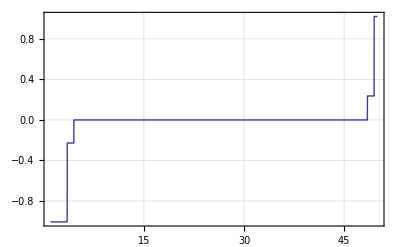

```mathematica
(* ==============================================*)
NoOfElements=50;
epsT=10^-1;
epsS=10^-1;

NTval=1+epsT;
NSval=3+epsS;

TTTval=1;

plotOpts ={PlotRange -> All, PlotStyle -> Thick, Frame -> True, GridLines -> Automatic};

(* ==============================================*)

Moment[lst_?VectorQ,level_?IntegerQ]:=Module[{len,ii,retVal},
len=Length[lst];
retVal=Sum[lst[[ii]]^level,{ii,1,len}];
Return[retVal];
];

(* ==============================================*)

mAnalyticFunc[level_?IntegerQ,nt_,ns_,ttt_]:=(ns+nt*(-ttt)^level);

(* ==============================================*)

sep="----------------";

(* ==============================================*)


(*
Print["..."];
Expand[cFunc31[3,TTT]*cFunc31[5,TTT]-0*cFunc31[4,TTT]^2]

tttMin=2;
tttMax=3.1;

Print[Plot[cFunc31[1,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[2,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[3,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[4,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[5,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];

Print["c2*c3/c5"];
Print[Plot[cFunc31[2,ttt]*cFunc31[3,ttt]/cFunc31[5,ttt],{ttt,tttMin,tttMax},Evaluate[plotOpts]]];

Print["c4/c2^2"];
Print[Plot[cFunc31[4,ttt]/cFunc31[2,ttt]^2,{ttt,tttMin,tttMax},Evaluate[plotOpts]]];

Print["c3*c5/c2^4"];
Print[Plot[cFunc31[5,ttt]*cFunc31[3,ttt]/cFunc31[2,ttt]^4,{ttt,tttMin,tttMax},Evaluate[plotOpts]]];
*)

(* ==============================================*)

IndexedFunc[lst_?VectorQ,idxVal_?NumericQ]:=Module[{len,idx},
len=Length[lst];
idx=Max[Min[Round[Re[idxVal]],len],1];
Return[lst[[idx]]];
];

(* ==============================================*)

Print["NT = ", NTval, ", NS = ",NSval];
Print["TTT = ", TTTval, ", N[TTT] = ", N[TTTval]];

(* ==============================================*)

Clear[NT,NS,TTT];
CkValList=Table[mAnalyticFunc[ii,NT,NS,TTT],{ii,1,6}];

Print["CkValList = ", CkValList // MatrixForm];
Print[sep];
Print[sep];
Print[sep];

ttt1Rule={TTT -> 1};
NTNSrule={NT -> NTval, NS -> NSval};

с6222=Simplify[(CkValList[[6]]/(CkValList[[2]]^3))];
Print["с6222 = ", с6222];
Print["с6222 = ", Simplify[с6222 /. ttt1Rule]];
с6222=Simplify[с6222 /. ttt1Rule]/.NTNSrule;
Print["с6222 = ", с6222];
Print[sep];

с532=Simplify[(CkValList[[5]]/(CkValList[[3]]*CkValList[[2]]))];
Print["с532 = ", с532];
Print["с532 = ", Simplify[с532 /. ttt1Rule]];
с532=Simplify[с532 /. ttt1Rule]/.NTNSrule;
Print["с532 = ", с532];
Print[sep];

с5221=Simplify[(CkValList[[5]]/(CkValList[[1]]*CkValList[[2]]^2))];
Print["с5221 = ", с5221];
Print["с5221 = ", Simplify[с5221 /. ttt1Rule]];
с5221=Simplify[с5221 /. ttt1Rule]/.NTNSrule;
Print["с5221 = ", с5221];
Print[sep];

с422=Simplify[(CkValList[[4]]/(CkValList[[2]]^2))];
Print["с422 = ", с422];
Print["с422 = ", Simplify[с422 /. ttt1Rule]];
с422=Simplify[с422 /. ttt1Rule]/.NTNSrule;
Print["с422 = ", с422];
Print[sep];

с112=Simplify[(CkValList[[1]]^2/(CkValList[[2]]))];
Print["с112 = ", с112];
Print["с112 = ", Simplify[с112 /. ttt1Rule]];
с112=Simplify[с112 /. ttt1Rule]/.NTNSrule;
Print["с112 = ", с112];
Print[sep];

c2=mAnalyticFunc[2,NT,NS,TTT];
Print["c2 = ", c2];
c2=Simplify[c2 /. ttt1Rule]/.NTNSrule;
Print["c2 = ", c2];
Print[sep];

(* ==============================================*)

a6222=1;
a532=1;
a5221=1;
a422=1;
a211=1;
a2=1;

(* ==============================================*)

lstFunc[lst_?VectorQ]:=Module[{len,ii,retVal,M1,M2,M3,M4,M5,M6,m541,m532,m5311,m5221,m52111,m511111,mm2,m422,m211,m6222},
M1=Moment[lst,1];
M2=Moment[lst,2];
M3=Moment[lst,3];
M4=Moment[lst,4];
M5=Moment[lst,5];
M6=Moment[lst,6];

m6222=a6222*(M6-с6222*M2^3)^2;
m532=a532*(M5-с532*M3*M2)^2;
m5221=a5221*(M5-с5221*M2^2*M1)^2;
m422=a422*M2*(M4-с422*M2^2)^2;
m211=a211*M2^3*(с112*M2-M1^2)^2;
mm2=a2*(M2-c2)^2;

retVal=m6222+(m532+m5221+m422+m211)*M2+mm2;
Return[retVal];
];

(* ==============================================*)

initValLst=Table[RandomReal[NormalDistribution[]],{ii,1,NoOfElements}];

Print["FindMinimum"];
sol=FindMinimum[lstFunc[xLst],{xLst,initValLst},WorkingPrecision -> 200, MaxIterations -> 2000];
xLstSol=xLst /. sol[[2]];
xLstSolSorted=Sort[xLstSol];
Print["sol[[1]] = ", N[sol[[1]]]];
(* Print["xLstSol = ", N[xLstSol]]; *)
Print["xLstSolSorted = ", N[xLstSolSorted]];
M1=Moment[xLstSol,1];
M2=Moment[xLstSol,2];
M3=Moment[xLstSol,3];
M4=Moment[xLstSol,4];
M5=Moment[xLstSol,5];

(* ==============================================*)

Print["M1 = ", N[M1], ", M2 = ", N[M2],", M3 = ", N[M3],", M4 = ", N[M4],", M5 = ", N[M5], ", (M3*M2/M5)*(c5/(c3*c2)) = ", N[(M3*M2/M5)*(c5/(c3*c2))],", (M4/M2^2)*(c2^2/c4) = ", N[(M4/M2^2)*(c2^2/c4)]];

Print[Plot[IndexedFunc[xLstSolSorted,idx],{idx,1,NoOfElements},Evaluate[plotOpts]]];

(* ==============================================*)
```